```mathematica
fy[x_] = (r2-(x-x0)^2)^(0.5)+y0
fyn[x_] = -(r2-(x-x0)^2)^(0.5)+y0
```

(r2-(x-x0)^2)^0.5+y0

-(r2-(x-x0)^2)^0.5+y0

```mathematica
Solve[(x1-x0)^2-(x2-x0)^2 == (y2-y0)^2-(y1-y0)^2 , x0]
```

{{x0→(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))}}

```mathematica
y0[x1_,y1_,x2_,y2_,x3_,y3_] = ((y3^2-y1^2-x1^2+x3^2)(x1-x2)+(x3-x1)(y2^2-y1^2-x1^2+x2^2))/(2*((y2-y1)(x3-x1)-(y3-y1)(x2-x1)))
```

((-x1+x3) (-x1^2+x2^2-y1^2+y2^2)+(x1-x2) (-x1^2+x3^2-y1^2+y3^2))/(2 ((-x1+x3) (-y1+y2)-(-x1+x2) (-y1+y3)))

```mathematica
x0[x1_,y1_,x2_,y2_] =(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))
```

(x1^2-x2^2-2 y0 y1+y1^2+2 y0 y2-y2^2)/(2 (x1-x2))

```mathematica
r2[x1_,y1_] = (x1-x0)^2+(y1-y0)^2
```

(-x0+x1)^2+(-y0+y1)^2

```mathematica
y0[-1,0,0,1,1,0]
x0[-1,0,0,1]/.{y0->y0[-1,0,0,1,1,0]}
r2 [-1,0]/.{x0->x0[-1,0,0,1]/.{y0->y0[-1,0,0,1,1,0]},y0->y0[-1,0,0,1,1,0]}
```

0

0

1

```mathematica
pts = {{2564563.71188291,8904070.39711587},{303875.60410714,2172207.97474591},{1431272.60708833,6127285.44496052}}
```

{{2.56456×10^6,8.90407×10^6},{303876.,2.17221×10^6},{1.43127×10^6,6.12729×10^6}}

```mathematica
yob=y0[pts[[1]][[1]],pts[[1]][[2]],pts[[2]][[1]],pts[[2]][[2]],pts[[3]][[1]],pts[[3]][[2]]]
xob=x0[pts[[1]][[1]],pts[[1]][[2]],pts[[2]][[1]],pts[[2]][[2]]]/.{y0->yob}
r2b=r2 [pts[[1]][[1]],pts[[1]][[2]]]/.{x0->xob,y0->yob}
```

-4.71409×10^6

3.19632×10^7

1.04974×10^15

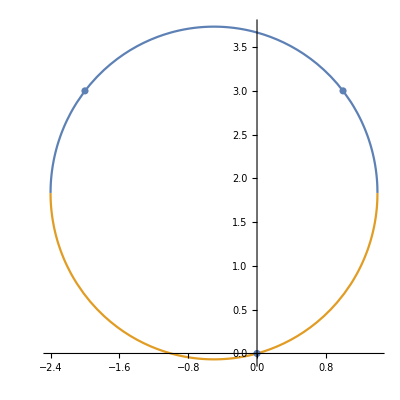

```mathematica
Show[Plot[{fy[x]/.{y0->yob, x0->xob,r2->r2b},fyn[x]/.{y0->yob, x0->xob,r2->r2b}},{x,xob-Sqrt[r2b],xob+Sqrt[r2b]},AspectRatio->1,PlotRange->{{xob-Sqrt[r2b],xob+Sqrt[r2b]},{yob-Sqrt[r2b],yob+Sqrt[r2b]}}],ListPlot[pts]]
```

```mathematica
fy2[r2_,x0_,y0_] = (r2-(x-x0)^2)^(0.5)+y0;
D[fy2[r2,x0,y0],r2]/.{x->u,r2-> x[2],x0-> x[1],y0-> x[0]}
D[fy2[r2,x0,y0],x0];
D[fy2[r2,x0,y0],y0];
fy2[x[2],x[1],x[0]]/.{x->u};
```

0.5/((-(u-x[1])^2+x[2])^0.5)

```mathematica
y0[xin3[0],yin3[0],xin3[1],yin3[1],xin3[2],yin3[2]]
x0[xin3[0],yin3[0],xin3[1],yin3[1]]
r2[xin3[0],yin3[0]]
```

((-xin3[0]+xin3[2]) (-xin3[0]^2+xin3[1]^2-yin3[0]^2+yin3[1]^2)+(xin3[0]-xin3[1]) (-xin3[0]^2+xin3[2]^2-yin3[0]^2+yin3[2]^2))/(2 ((-xin3[0]+xin3[2]) (-yin3[0]+yin3[1])-(-xin3[0]+xin3[1]) (-yin3[0]+yin3[2])))

(xin3[0]^2-xin3[1]^2-2 y0 yin3[0]+yin3[0]^2+2 y0 yin3[1]-yin3[1]^2)/(2 (xin3[0]-xin3[1]))

(-x0+xin3[0])^2+(-y0+yin3[0])^2